## Graph algorithms

There is sophisticated built-in support for graphs and graph algorithms

There are lots of built-in graphs obtainable using GraphData, e.g.

```mathematica
GraphData[]
```

{AGraph,{Andrasfai,4},{Andrasfai,5},{Andrasfai,6},{Andrasfai,7},{Andrasfai,8},{Andrasfai,9},{Andrasfai,10},6821,{ZeroTwoNonbipartite,{7,48}},{ZeroTwoNonbipartite,{7,49}},{ZeroTwoNonbipartite,{7,50}},{ZeroTwoNonbipartite,{7,52}},{ZeroTwoNonbipartite,{7,53}},{ZeroTwoNonbipartite,{7,54}},{ZeroTwoNonbipartite,{7,55}},{ZeroTwoNonbipartite,{7,56}}}
 |  |  |  |

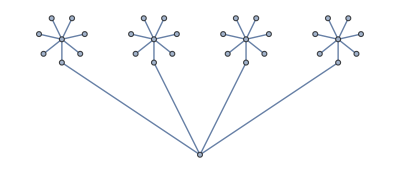

```mathematica
g=GraphData[{"BananaTree", {4, 8}}]
```

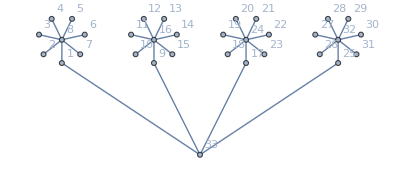

```mathematica
Graph[g,VertexLabels->Automatic]
```

Let’s perform a depth-first search on this tree

We start with the root node (33) in our case, and visit each node in the graph by first visiting all the children of a given node before visiting any of its siblings

```mathematica
rootNode=33;
```

We will need to find the neighbors of a given node:

```mathematica
AdjacencyList[g,rootNode]
```

{1,9,17,25}

We also don’t want to visit our parent, so we will use Cases and Except to skip items

```mathematica
AdjacencyList[g,1]
```

{8,33}

```mathematica
Cases[AdjacencyList[g,1],Except[33]]
```

{8}

```mathematica
depthFirst[graph_,node_,parent_]:=Module[{adj},
Print["Visiting ", node];
adj=Cases[AdjacencyList[graph,node],Except[parent]];
Scan[depthFirst[graph,#,node]&,adj]
]
depthFirst[graph_,root_]:=depthFirst[graph,root,root]
```

```mathematica
depthFirst[g,33]
```

Visiting 33

Visiting 1

Visiting 8

Visiting 2

Visiting 3

Visiting 4

Visiting 5

Visiting 6

Visiting 7

Visiting 9

Visiting 16

Visiting 10

Visiting 11

Visiting 12

Visiting 13

Visiting 14

Visiting 15

Visiting 17

Visiting 24

Visiting 18

Visiting 19

Visiting 20

Visiting 21

Visiting 22

Visiting 23

Visiting 25

Visiting 32

Visiting 26

Visiting 27

Visiting 28

Visiting 29

Visiting 30

Visiting 31

```mathematica
DepthFirstScan[g,33,{"PrevisitVertex"->(Print["Visiting ",#]&)}];
```

Visiting 33

Visiting 1

Visiting 8

Visiting 2

Visiting 3

Visiting 4

Visiting 5

Visiting 6

Visiting 7

Visiting 9

Visiting 16

Visiting 10

Visiting 11

Visiting 12

Visiting 13

Visiting 14

Visiting 15

Visiting 17

Visiting 24

Visiting 18

Visiting 19

Visiting 20

Visiting 21

Visiting 22

Visiting 23

Visiting 25

Visiting 32

Visiting 26

Visiting 27

Visiting 28

Visiting 29

Visiting 30

Visiting 31

```mathematica
BreadthFirstScan[g,33,{"PrevisitVertex"->(Print["Visiting ",#]&)}];
```

Visiting 33

Visiting 1

Visiting 9

Visiting 17

Visiting 25

Visiting 8

Visiting 16

Visiting 24

Visiting 32

Visiting 2

Visiting 3

Visiting 4

Visiting 5

Visiting 6

Visiting 7

Visiting 10

Visiting 11

Visiting 12

Visiting 13

Visiting 14

Visiting 15

Visiting 18

Visiting 19

Visiting 20

Visiting 21

Visiting 22

Visiting 23

Visiting 26

Visiting 27

Visiting 28

Visiting 29

Visiting 30

Visiting 31

```mathematica
FindShortestPath[g,2,21]
```

{2,8,1,33,17,24,21}

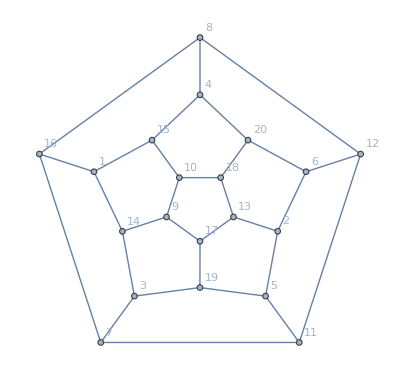

```mathematica
g=Graph[PolyhedronData["Dodecahedron","SkeletonGraph"],VertexLabels->Automatic]
```

```mathematica
path=FindHamiltonianPath[g]
```

{13,18,10,15,4,20,6,2,5,19,3,7,11,12,8,16,1,14,9,17}

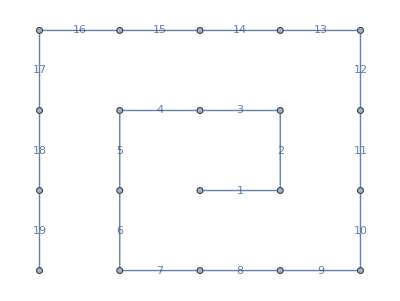

```mathematica
pg=PathGraph[path,VertexLabels->None,EdgeLabels->"Index"]
```

```mathematica
edgelabels=MapIndexed[#1->#2⟦1⟧&,EdgeList[pg]]
```

{13<->18→1,18<->10→2,10<->15→3,15<->4→4,4<->20→5,20<->6→6,6<->2→7,2<->5→8,5<->19→9,19<->3→10,3<->7→11,7<->11→12,11<->12→13,12<->8→14,8<->16→15,16<->1→16,1<->14→17,14<->9→18,9<->17→19}

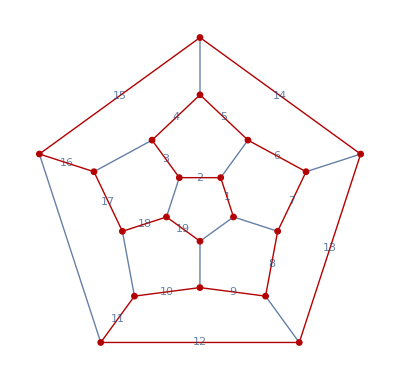

```mathematica
HighlightGraph[g,pg,VertexLabels->None,EdgeLabels->edgelabels]
```